```mathematica
f[x_]:=Piecewise[{{1+x,x<0},{1-x,x>=0}}]
```

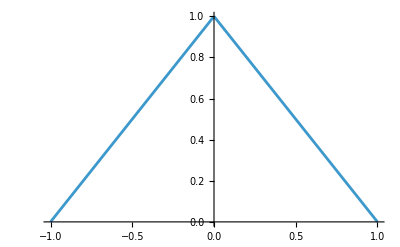

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
F[x_]=Integrate[f[x],x]
```

Piecewise[{{x+x^2/2, x≤0}, {x-x^2/2, True}}]

```mathematica
F[x]
```

Piecewise[{{x+x^2/2, x≤0}, {x-x^2/2, True}}]

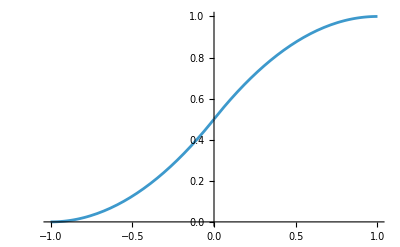

```mathematica
Plot[F[x]+1/2,{x,-1,1}]
```

```mathematica
Inverse[F[x]]
```

(Piecewise[{{x+x^2/2, x≤0}, {x-x^2/2, True}}])

```mathematica
InverseFunction
```

```mathematica
Y:=With[{x=RandomReal[]},If[x<1/2,-1+Sqrt[2*x],1-Sqrt[2-2*x]]]
```

```mathematica
Y&/@Range[100]
```

{-0.590915,-0.675095,0.303534,0.440596,0.542225,-0.96374,0.568746,0.118826,-0.370084,0.346718,0.508436,-0.489437,0.743609,-0.553809,0.269674,0.100287,0.0910583,-0.875947,-0.117403,0.620017,0.0520525,0.0499727,-0.442308,-0.348338,-0.283965,-0.149258,0.073559,-0.58735,0.787556,-0.0145601,0.0320132,-0.130345,-0.0908926,-0.321289,-0.486976,0.442892,0.00202789,-0.137807,0.566877,0.0389967,0.751203,-0.452787,0.122261,-0.148769,-0.327666,-0.188212,-0.85209,-0.0730898,0.107412,0.368235,-0.138313,-0.876201,0.683947,0.448936,0.44057,-0.399346,-0.344488,0.000608832,0.339877,0.020167,-0.0967325,-0.549879,-0.0074674,0.00758917,0.0210608,-0.297009,0.354969,0.163508,0.262175,0.30557,-0.149549,-0.85201,0.548377,-0.0389636,-0.100352,-0.460083,-0.909158,0.175658,-0.709735,-0.716122,-0.202297,0.266945,-0.428649,0.408839,0.320703,0.122767,-0.189753,-0.101843,0.418845,-0.679612,0.530258,0.727366,0.264306,0.30951,-0.0194517,0.160582,0.780413,0.190573,0.34636,0.19577}

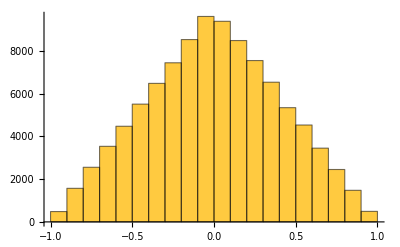

```mathematica
Histogram[Y&/@Range[100000]]
```